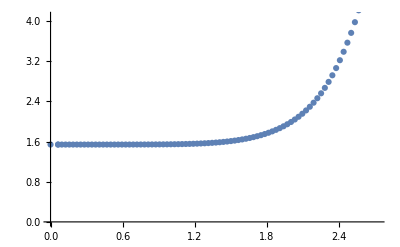

```mathematica
f={{0,8.104713},{0.062500,8.079927},{0.062500,8.079927},{0.093750,8.066607},{0.125000,8.052463},{0.156250,8.037415},{0.187500,8.021407},{0.218750,8.004400},{0.250000,7.986369},{0.281250,7.967292},{0.312500,7.947156},{0.343750,7.925949},{0.375000,7.903665},{0.406250,7.880298},{0.437500,7.855845},{0.468750,7.830303},{0.500000,7.803672},{0.531250,7.775953},{0.562500,7.747146},{0.593750,7.717254},{0.625000,7.686281},{0.656250,7.654233},{0.687500,7.621116},{0.718750,7.586937},{0.750000,7.551707},{0.781250,7.515438},{0.812500,7.478144},{0.843750,7.439842},{0.875000,7.400552},{0.906250,7.360298},{0.937500,7.319106},{0.968750,7.277008},{1.000000,7.234041},{1.031250,7.190247},{1.062500,7.145674},{1.093750,7.100377},{1.125000,7.054417},{1.156250,7.007864},{1.187500,6.960796},{1.218750,6.913302},{1.250000,6.865479},{1.281250,6.817436},{1.312500,6.769294},{1.343750,6.721186},{1.375000,6.673259},{1.406250,6.625676},{1.437500,6.578613},{1.468750,6.532266},{1.500000,6.486850},{1.531250,6.442597},{1.562500,6.399765},{1.593750,6.358634},{1.625000,6.319509},{1.656250,6.282726},{1.687500,6.248652},{1.718750,6.217685},{1.750000,6.190265},{1.781250,6.166870},{1.812500,6.148025},{1.843750,6.134304},{1.875000,6.126336},{1.906250,6.124813},{1.937500,6.130493},{1.968750,6.144209},{2.000000,6.166879},{2.031250,6.199510},{2.062500,6.243217},{2.093750,6.299223},{2.125000,6.368880},{2.156250,6.453678},{2.187500,6.555255},{2.218750,6.675404},{2.250000,6.816078},{2.281250,6.979371},{2.312500,7.167474},{2.343750,7.382572},{2.375000,7.626666},{2.406250,7.901335},{2.437500,8.207753},{2.468750,8.547417},{2.500000,8.923138},{2.531250,9.339242},{2.562500,9.801469},{2.593750,10.316864},{2.625000,10.892747},{2.656250,11.532512},{2.687500,12.222618},{2.718750,12.900751}};
ff={{0,6.565129},{0.062500,6.540343},{0.062500,6.540343},{0.093750,6.527022},{0.125000,6.512877},{0.156250,6.497826},{0.187500,6.481815},{0.218750,6.464805},{0.250000,6.446767},{0.281250,6.427683},{0.312500,6.407537},{0.343750,6.386318},{0.375000,6.364018},{0.406250,6.340630},{0.437500,6.316151},{0.468750,6.290576},{0.500000,6.263904},{0.531250,6.236132},{0.562500,6.207261},{0.593750,6.177290},{0.625000,6.146220},{0.656250,6.114052},{0.687500,6.080788},{0.718750,6.046431},{0.750000,6.010984},{0.781250,5.974453},{0.812500,5.936841},{0.843750,5.898157},{0.875000,5.858407},{0.906250,5.817603},{0.937500,5.775755},{0.968750,5.732877},{1.000000,5.688985},{1.031250,5.644098},{1.062500,5.598239},{1.093750,5.551431},{1.125000,5.503707},{1.156250,5.455098},{1.187500,5.405645},{1.218750,5.355393},{1.250000,5.304392},{1.281250,5.252701},{1.312500,5.200386},{1.343750,5.147519},{1.375000,5.094185},{1.406250,5.040475},{1.437500,4.986494},{1.468750,4.932355},{1.500000,4.878186},{1.531250,4.824126},{1.562500,4.770332},{1.593750,4.716973},{1.625000,4.664237},{1.656250,4.612328},{1.687500,4.561471},{1.718750,4.511913},{1.750000,4.463923},{1.781250,4.417794},{1.812500,4.373847},{1.843750,4.332432},{1.875000,4.293932},{1.906250,4.258762},{1.937500,4.227379},{1.968750,4.200276},{2.000000,4.177995},{2.031250,4.161126},{2.062500,4.150310},{2.093750,4.146248},{2.125000,4.149706},{2.156250,4.161514},{2.187500,4.182582},{2.218750,4.213895},{2.250000,4.256526},{2.281250,4.311637},{2.312500,4.380483},{2.343750,4.464406},{2.375000,4.564827},{2.406250,4.683221},{2.437500,4.821066},{2.468750,4.979746},{2.500000,5.160408},{2.531250,5.363774},{2.562500,5.590094},{2.593750,5.839498},{2.625000,6.112643},{2.656250,6.411001},{2.687500,6.736850},{2.718750,7.093308}};
F1=f-ff*Table[{0,1},{i,0,87}];
ListPlot[F1]
```

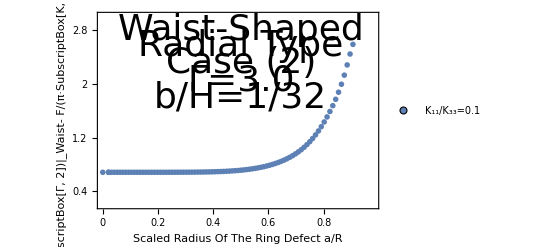

```mathematica
FF1=F1*Table[{1/3,4/9},{i,0,87}];
ListPlot[{FF1},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{0.4,1.2,2,2.8},None},{{0,0.2, 0.4, 0.6, 0.8},None}}, PlotRange->{{0,0.98},{0.2,3.0}},FrameLabel->{{"F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Waist- F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Cylinder", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1"},LegendMarkers->{{Graphics[Disk[]],12}}],{Right, Bottom}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{0.5,2.8}],Text[Style["Radial Type",Directive[Black,36]],{0.5,2.55}],Text[Style["Case (2)",Directive[Black,36]],{0.5,2.3}],Text[Style["Γ=3.0",Directive[Black,36]],{0.5,2.05}],Text[Style["b/H=1/32",Directive[Black,36]],{0.5,1.8}]}]
```